# Liver slices MFA

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
OpenDBConnection[]
```

## Set paths

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\code\liver-flux-analysis\flux-analysis-liver-2023-01-24

```mathematica
patientId="L002";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L002

```mathematica
modelDir="C:\\code\\liver-flux-models\\Models\\liverModel_2_openFluxExport";
```

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
{net,atomMaps,targets}=OpenFLUXImport[FileNameJoin[{modelDir,"liver-model_openflux.txt"}]];
```

```mathematica
net
```

<MetabolicNetwork, 91 reactions>

```mathematica
Length[atomMaps]
```

91

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 36 boundary fluxes>

```mathematica
targets
```

{<akg_m{(12345)}>,<akg_c{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<arg-L_l{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<f6p_c{(123456)}>,<g1p_r{(123456)}>,<g6p_c{(123456)}>,<g6p_r{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>}

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID[FileNameJoin[{modelDir,"substrate-distributions.txt"}]]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.99}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.99}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.99}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.99}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.99}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.99}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.99}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.99}]}

#### Check atom map

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMaps]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmaps=BoundaryAtomMaps[net,atomMaps];
bmaps//Length
```

36

### Symmetry

Note: this will not account for any symmeric metabolites in model that are absent from the database

```mathematica
symmetry=GetSymmetryMap[atomMaps]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTable[FileNameJoin[{lcmsDataDir,"L002",experimentId<>".tsv"}]];
```

### Sample annotations

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{fresh medium 0h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 0h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{,plasma,,L002,,human}}

### Targets

Define targets from measured metabolites present in the model
(Now imported from OpenFlux model file instead, see above)

```mathematica
(*targets=Cases[MetaboliteEMUs[atomMaps],EMU[Metabolite[Alternatives@@Flatten[measuredMetIds],__],_]](*
```

{<acrn_c{(12)}>,<acrn_m{(12)}>,<akg_c{(12345)}>,<akg_m{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<arg-L_l{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<f6p_c{(123456)}>,<g1p_r{(123456)}>,<g6p_c{(123456)}>,<g6p_r{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<gthrd_c{(123456789a)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>}

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{acrn,ahcys,asn-L,creat,crn,dhdascb,fru,g3pc,gchola,glcnt,glcur,gthrd,gudac,his-L,ile-L,imp,inost,Lcystin,leu-L,lys-L,met-L,nad,nadh,phe-L,pmtcrn,pro-L,r5p,sbt-D,thr-L,trp-L,tyr-L,udpg,ump,urate,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

14

List of unique names for measurements, for use with GAMS

```mathematica
measuredMetNames=Map[ListToString[#,"__"]&,measuredMetIds]
```

{glc-D,ala-L,arg-L,asp-L,gln-L,ser-L,mal-L,f6p__g1p__g6p,orn,citr-L,glyc3p,akg,glu-L,gly}

### EMU mixing matrix

Create (measurements x targets) mixing matrix

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[
Thread[{i,Flatten[Position[targets,EMU[Metabolite[Alternatives@@measuredMetIds⟦i⟧,_,_],_]]]}],
1]],
{i,Length[measuredMetIds]}],
{Length[measuredMetIds],Length[targets]}]
```

SparseArray[<26>, {14, 26}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

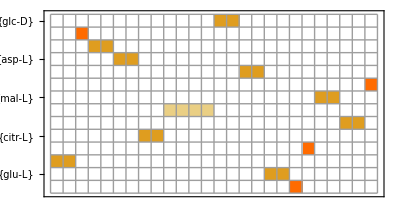

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetIds]],measuredMetIds}],None},Mesh->True]
```

List of measurement-target mappings

```mathematica
TableForm[Replace[
NonZeroIndices[emuMixing],
{i_,j_}:>{measuredMetNames⟦i⟧,targets⟦j⟧},{1}]]
```

glc-D | <glc-D_c{(123456)}>
glc-D | <glc-D_r{(123456)}>
ala-L | <ala-L_c{(123)}>
arg-L | <arg-L_c{(123456)}>
arg-L | <arg-L_l{(123456)}>
asp-L | <asp-L_c{(1234)}>
asp-L | <asp-L_m{(1234)}>
gln-L | <gln-L_c{(12345)}>
gln-L | <gln-L_m{(12345)}>
ser-L | <ser-L_c{(123)}>
mal-L | <mal-L_c{(1234)}>
mal-L | <mal-L_m{(1234)}>
f6p__g1p__g6p | <f6p_c{(123456)}>
f6p__g1p__g6p | <g1p_r{(123456)}>
f6p__g1p__g6p | <g6p_c{(123456)}>
f6p__g1p__g6p | <g6p_r{(123456)}>
orn | <orn_c{(12345)}>
orn | <orn_m{(12345)}>
citr-L | <citr-L_c{(123456)}>
citr-L | <citr-L_m{(123456)}>
glyc3p | <glyc3p_c{(123)}>
akg | <akg_m{(12345)}>
akg | <akg_c{(12345)}>
glu-L | <glu-L_c{(12345)}>
glu-L | <glu-L_m{(12345)}>
gly | <gly_c{(12)}>

## Uptake/release data

### Concentration estimates from medium fold changes

This reflects net balance, not directional fluxes.

Fresh medium concentrations (M)

```mathematica
initConc=Rest[Import["C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\williams_E.txt","TSV"]];
initConc=Cases[initConc,{Alternatives@@(MetaboliteID/@InputMetabolites[net]),_}];
{measuredBoundaryIds,initConc}=Transpose[initConc];
measuredBoundaryIds=Partition[measuredBoundaryIds,1];
```

Fold changes fresh (incubated) medium, paired

```mathematica
Extract[sampleIds,
Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]
```

{H_MS_U_FM24h_1,H_MS_U_FM24h_2,H_MS_U_FM24h_3}

```mathematica
mediumFoldchange=Block[{metIndex,freshIndex,spentIndex,freshPa,spentPa},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"12C",_,Except[1],_}]];
freshPa=Map[Normal[#]⟦1⟧&,measuredMIDs⟦metIndex,freshIndex⟧,{2}];
spentPa=Map[Normal[#]⟦1⟧&,measuredMIDs⟦metIndex,spentIndex⟧,{2}];
spentPa/(Mean/@freshPa)];
```

```mathematica
TableForm[mediumFoldchange,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.707058 | 0.649568 | 0.637019
{arg-L} | 0.649441 | 0.896945 | 1.26799
{asp-L} | 0.708741 | 0.619282 | 0.686753
{gln-L} | 0.775106 | 0.677992 | 0.691322
{gly} | 0.772581 | 0.668197 | 0.579593
{ser-L} | 0.717339 | 0.620893 | 0.566426
{glc-D} | 0.931016 | 0.842854 | 0.792857

Convert to concentration differences

```mathematica
mediumConcDiff=initConc*(mediumFoldchange-1);
```

In um

```mathematica
TableForm[mediumConcDiff*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -295.872 | -353.936 | -366.611
{arg-L} | -83.0826 | -24.4241 | 63.5144
{asp-L} | -65.8246 | -86.0422 | -70.7937
{gln-L} | -449.787 | -644.016 | -617.355
{gly} | -151.688 | -221.312 | -280.411
{ser-L} | -26.9093 | -36.091 | -41.2762
{glc-D} | -765.722 | -1744.32 | -2299.29

### As mean +/- std dev

```mathematica
mediumConcDiffMean=Mean/@mediumConcDiff;
```

```mathematica
mediumConcDiffSD=StandardDeviation/@mediumConcDiff;
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.806 | 37.7187
{arg-L} | -14.6641 | 73.7842
{asp-L} | -74.2202 | 10.5353
{gln-L} | -570.386 | 105.289
{gly} | -217.804 | 64.4332
{ser-L} | -34.7588 | 7.27549
{glc-D} | -1603.11 | 776.475

### Add concentrations from clinical chemistry

Add lactate estimate (rough)

```mathematica
AppendTo[measuredBoundaryIds,{"lac-L"}];
AppendTo[mediumConcDiffMean,Mean[{1.0,1.5}]*0.001];
AppendTo[mediumConcDiffSD,StandardDeviation[{1.0,1.5}]*0.001];
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.806 | 37.7187
{arg-L} | -14.6641 | 73.7842
{asp-L} | -74.2202 | 10.5353
{gln-L} | -570.386 | 105.289
{gly} | -217.804 | 64.4332
{ser-L} | -34.7588 | 7.27549
{glc-D} | -1603.11 | 776.475
{lac-L} | 1250. | 353.553

### Calculate net uptake/release fluxes

Convert to fluxes (positive = release)

```mathematica
mediumVolume=0.0013;
cultureTime=24;
```

In nmol / h

```mathematica
TableForm[
Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*mediumVolume/cultureTime*10^9,
TableHeadings->{measuredBoundaryIds,{"mean","stddev"}}]
```

| mean | stddev
{ala-L} | -18.352 | 2.04309
{arg-L} | -0.794304 | 3.99665
{asp-L} | -4.02026 | 0.570664
{gln-L} | -30.8959 | 5.70315
{gly} | -11.7977 | 3.49013
{ser-L} | -1.88277 | 0.394089
{glc-D} | -86.8352 | 42.0591
{lac-L} | 67.7083 | 19.1508

Map uptake/release fluxes to EMU fluxes

```mathematica
Block[{rules},
measFluxNames=First/@measuredBoundaryIds;
rules=Join@@Table[
Join[
Cases[BoundaryMetabolites[bnet],Metabolite[m,"Input",_]:>{m,m<>"_IN",-1}],
Cases[BoundaryMetabolites[bnet],Metabolite[m,"Output",_]:>{m,m<>"_OUT",1}]],
{m,measFluxNames}];
measReactions=Union[rules⟦All,2⟧];
fluxMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[rules⟦All,1⟧,measFluxNames],
ReindexList[rules⟦All,2⟧,measReactions]}],
rules⟦All,3⟧]],
{Length[measFluxNames],Length[measReactions]}]]
```

SparseArray[<12>, {8, 12}]

### Calculate absolute release fluxes (TODO)

This slould probably be done by adding an “output” compartment to the model.

```mathematica
spentMediumMIDs=Block[{metIndex,freshIndex,spentIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"13C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"13C",_,Except[1],_}]];
metIndex]
```

{2,3,4,5,14,6,1,Missing}

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{91,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

78

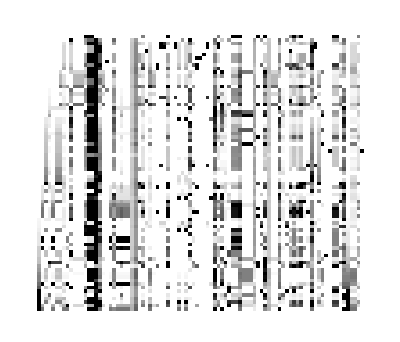

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]
```

{{<Reaction ACONTm(rev)>,cit_m <=> icit_m},{<Reaction ASPTAm(rev)>,glu-L_m + oaa_m <=> akg_m + asp-L_m},{<Reaction ATPtm(rev)>,adp_c + atp_m <=> adp_m + atp_c},{<Reaction GHMT2r(rev)>,ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c},{<Reaction GLUNm(rev)>,gln-L_m + h2o_m <=> glu-L_m + nh4_m},{<Reaction ICDHxm(rev)>,icit_m + nad_m <=> akg_m + co2_m + nadh_m},{<Reaction LDH_L(rev)>,h_c + nadh_c + pyr_c <=> lac-L_c + nad_c},{<Reaction MDHm(rev)>,mal-L_m + nad_m <=> h_m + nadh_m + oaa_m},{<Reaction PYRt2m(rev)>,pyr_c <=> pyr_m}}

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[energy,Input,Boundary],Metabolite[glyc,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[pi,Output,Boundary]}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMaps,bmaps,{"C"},targets,symmetry];
Length[emuReactions]
```

959

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[108,<ser-L_c{(3)}>,<2amac_c{(3)}>,1],EMUReaction[132,<oaa_m{(124)}>,<mal-L_m{(124)}>,1],EMUReaction[61,<gln-L_c{(3)}>,<gln-L_m{(3)}>,1],EMUReaction[37,<asp-L_m{(2)}>,<asp-L_c{(2)}>,1],EMUReaction[135,<3pg_c{(1)}>,<13dpg_c{(1)}>,1],EMUReaction[75,<pyr_c{(23)}>,<lac-L_c{(23)}>,1],EMUReaction[121,<g3p_c{(1)}>,<fdp_c{(4)}>,1],EMUReaction[116,<glu-L_c{(1234)}>,<akg_c{(1234)}>,1],EMUReaction[136,<2pg_c{(23)}>,<3pg_c{(23)}>,1],EMUReaction[62,<glu-L_m{(35)}>,<akg_m{(35)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

489

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["glc-D",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

glc-D_IN | <glc-D_i{(1)}> | <glc-D_c{(1)}>
GLCter_f | <glc-D_r{(1)}> | <glc-D_c{(1)}>
glc-D_IN | <glc-D_i{(2)}> | <glc-D_c{(2)}>
GLCter_f | <glc-D_r{(2)}> | <glc-D_c{(2)}>
glc-D_IN | <glc-D_i{(3)}> | <glc-D_c{(3)}>
GLCter_f | <glc-D_r{(3)}> | <glc-D_c{(3)}>
glc-D_IN | <glc-D_i{(4)}> | <glc-D_c{(4)}>
GLCter_f | <glc-D_r{(4)}> | <glc-D_c{(4)}>
glc-D_IN | <glc-D_i{(5)}> | <glc-D_c{(5)}>
GLCter_f | <glc-D_r{(5)}> | <glc-D_c{(5)}>
glc-D_IN | <glc-D_i{(6)}> | <glc-D_c{(6)}>
GLCter_f | <glc-D_r{(6)}> | <glc-D_c{(6)}>
glc-D_IN | <glc-D_i{(12)}> | <glc-D_c{(12)}>
GLCter_f | <glc-D_r{(12)}> | <glc-D_c{(12)}>
glc-D_IN | <glc-D_i{(23)}> | <glc-D_c{(23)}>
GLCter_f | <glc-D_r{(23)}> | <glc-D_c{(23)}>
glc-D_IN | <glc-D_i{(45)}> | <glc-D_c{(45)}>
GLCter_f | <glc-D_r{(45)}> | <glc-D_c{(45)}>
glc-D_IN | <glc-D_i{(56)}> | <glc-D_c{(56)}>
GLCter_f | <glc-D_r{(56)}> | <glc-D_c{(56)}>
glc-D_IN | <glc-D_i{(123)}> | <glc-D_c{(123)}>
GLCter_f | <glc-D_r{(123)}> | <glc-D_c{(123)}>
glc-D_IN | <glc-D_i{(456)}> | <glc-D_c{(456)}>
GLCter_f | <glc-D_r{(456)}> | <glc-D_c{(456)}>
glc-D_IN | <glc-D_i{(123456)}> | <glc-D_c{(123456)}>
GLCter_f | <glc-D_r{(123456)}> | <glc-D_c{(123456)}>
G6PPer_f | <g6p_r{(1)}> | <glc-D_r{(1)}>
G6PPer_f | <g6p_r{(2)}> | <glc-D_r{(2)}>
G6PPer_f | <g6p_r{(3)}> | <glc-D_r{(3)}>
G6PPer_f | <g6p_r{(4)}> | <glc-D_r{(4)}>
G6PPer_f | <g6p_r{(5)}> | <glc-D_r{(5)}>
G6PPer_f | <g6p_r{(6)}> | <glc-D_r{(6)}>
G6PPer_f | <g6p_r{(12)}> | <glc-D_r{(12)}>
G6PPer_f | <g6p_r{(23)}> | <glc-D_r{(23)}>
G6PPer_f | <g6p_r{(45)}> | <glc-D_r{(45)}>
G6PPer_f | <g6p_r{(56)}> | <glc-D_r{(56)}>
G6PPer_f | <g6p_r{(123)}> | <glc-D_r{(123)}>
G6PPer_f | <g6p_r{(456)}> | <glc-D_r{(456)}>
G6PPer_f | <g6p_r{(123456)}> | <glc-D_r{(123456)}>

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 211 internals, 39 substrates, 0 condensations >
2 | <EMUEquation (2), 146 internals, 25 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 16 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 14 internals, 4 substrates, 2 condensations >

## Substrates

### Check substrate purity against fresh medium MIDs

```mathematica
freshMediumMIDs=Block[{metIndex,freshIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"13C",_,Except[1],_}]];
Map[Normal[MIDNormalize[#]]&,measuredMIDs⟦metIndex,freshIndex⟧,{2}]];
```

```mathematica
TableForm[Mean/@freshMediumMIDs,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.00334087 | 0.000318284 | 0.014643 | 0.981698 |  |  | 
{arg-L} | 0.00128799 | 0.0000125828 | 0. | 0. | 0.000566733 | 0.0386296 | 0.959503
{asp-L} | 0.000661918 | 0. | 0.000258311 | 0.0294335 | 0.969646 |  | 
{gln-L} | 0.000059953 | 0.000035674 | 0.0000889447 | 0.000448628 | 0.0293009 | 0.970066 | 
{gly} | 0.0166696 | 0.00601337 | 0.977317 |  |  |  | 
{ser-L} | 0. | 0. | 0.0249283 | 0.975072 |  |  | 
{glc-D} | 0.00283041 | 0. | 0. | 0. | 0.000707877 | 0.0548791 | 0.941583

Estimates tracer 13C enrichment from measured M+n fraction, as x_n^(1/n)

```mathematica
Table[
Power[Last[x],1/(Length[x]-1)],
{x,Mean/@freshMediumMIDs}]
```

{0.993862,0.993134,0.992324,0.99394,0.988593,0.991621,0.990018}

### Specify input isotopomers (tracers)

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

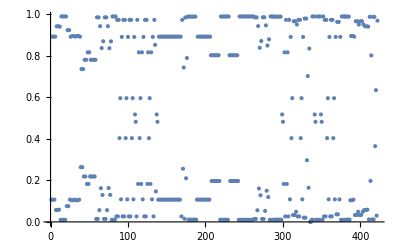
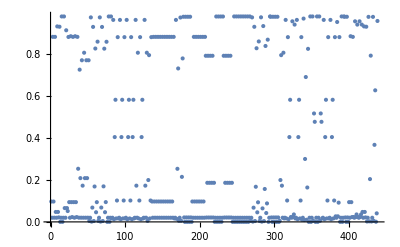
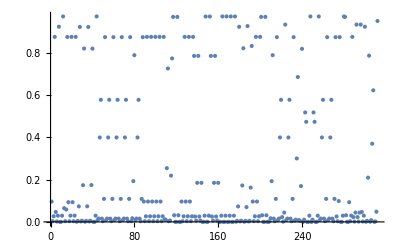
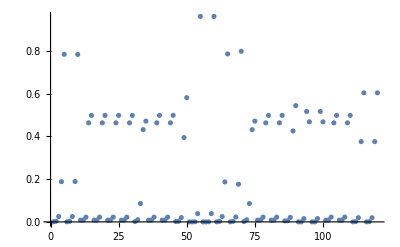
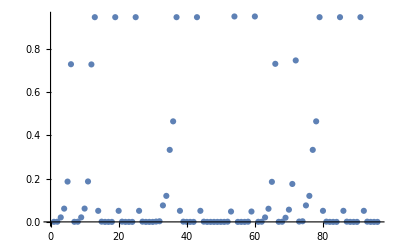
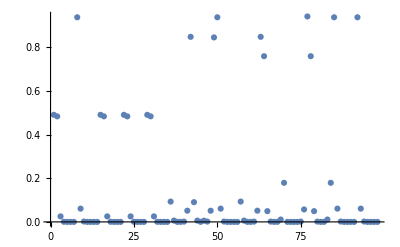

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],"gams"}]
```

C:\code\liver-flux-analysis\flux-analysis-liver-2023-01-24\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.03;
```

```mathematica
Directory[]
```

C:\code\liver-flux-analysis\flux-analysis-liver-2023-01-24

```mathematica
StringTemplate["`1` and `2`"][ "A","B"]
```

A and B

### Generate optimization model

MIDs to fit

```mathematica
midsToFit=Block[{sampleIndex},
sampleIndex=Flatten[Position[sampleInfo,{"tissue slice 24h",_,"13C",_,Except[1],_}]];
Map[First[MIDNormalize[#]]&,measuredMIDs⟦All,sampleIndex⟧,{2}]];
```

Export model file

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes *)
measFluxNames,measReactions,mediumConcDiffMean*mediumVolume/cultureTime*10^9,mediumConcDiffSD*mediumVolume/cultureTime*10^9,fluxMixing,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
RandomFluxState[10],
"FluxCI"->"]
```

C:\code\liver-flux-analysis\flux-analysis-liver-2023-01-24\gams\liver-model.gms

### Run GAMS

From command line ...

## Import GAMS solutions

### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<22>, {14, 26}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

glc-D | <glc-D_c{(123456)}> | 0.814264
glc-D | <glc-D_r{(123456)}> | 0.185736
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 0.251971
arg-L | <arg-L_l{(123456)}> | 0.748029
asp-L | <asp-L_c{(1234)}> | 0.315334
asp-L | <asp-L_m{(1234)}> | 0.684666
gln-L | <gln-L_m{(12345)}> | 1.
ser-L | <ser-L_c{(123)}> | 1.
mal-L | <mal-L_c{(1234)}> | 0.29431
mal-L | <mal-L_m{(1234)}> | 0.70569
f6p__g1p__g6p | <f6p_c{(123456)}> | 0.263817
f6p__g1p__g6p | <g1p_r{(123456)}> | 0.323073
f6p__g1p__g6p | <g6p_r{(123456)}> | 0.41311
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glyc3p | <glyc3p_c{(123)}> | 1.
akg | <akg_c{(12345)}> | 1.
glu-L | <glu-L_c{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.

### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

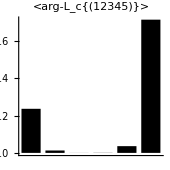
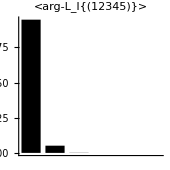

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["arg-L",_,_],{{{1,2,3,4,5}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

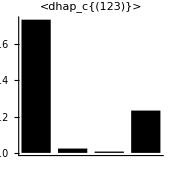
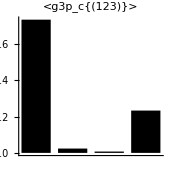
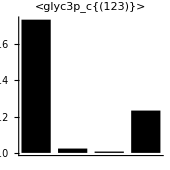

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p"|"dhap"|"glyc3p",__],{{{1,2,3}}}]]];
Table[ 
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

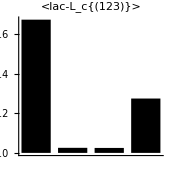

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["lac-L",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

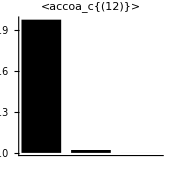
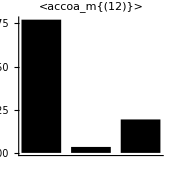

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixingGams;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

```mathematica
TableForm[fittedMIDs,TableHeadings->{measuredMetNames,None}]
```

glc-D | 0.502809 | 0.0326295 | 0.000882347 | 0.0000217213 | 0.000668198 | 0.0264565 | 0.436533
ala-L | 0.372027 | 0.0122541 | 0.0182361 | 0.597483 |  |  | 
arg-L | 0.759668 | 0.0497962 | 0.00136049 | 0.0000762038 | 0.00285609 | 0.0603619 | 0.125881
asp-L | 0.319314 | 0.119256 | 0.128861 | 0.109558 | 0.32301 |  | 
gln-L | 0.0287042 | 0.0150504 | 0.0163928 | 0.00897978 | 0.046041 | 0.884832 | 
ser-L | 0.569293 | 0.0470349 | 0.136269 | 0.247403 |  |  | 
mal-L | 0.296139 | 0.145348 | 0.162258 | 0.0893967 | 0.306858 |  | 
f6p__g1p__g6p | 0.864036 | 0.0560796 | 0.00236225 | 0.0279631 | 0.000976257 | 0.00278538 | 0.0457971
orn | 0.236241 | 0.0127756 | 0.000283712 | 0.000731397 | 0.0360562 | 0.713912 | 
citr-L | 0.227297 | 0.0212353 | 0.000756618 | 0.000714449 | 0.0347189 | 0.688251 | 0.0270266
glyc3p | 0.735195 | 0.0239265 | 0.00733506 | 0.233544 |  |  | 
akg | 0.249452 | 0.130794 | 0.142385 | 0.0705762 | 0.0307466 | 0.376046 | 
glu-L | 0.249452 | 0.130794 | 0.142385 | 0.0705762 | 0.0307466 | 0.376046 | 
gly | 0.334864 | 0.020269 | 0.644867 |  |  |  |

Compare fitted MIDs (gray) with measured (black)

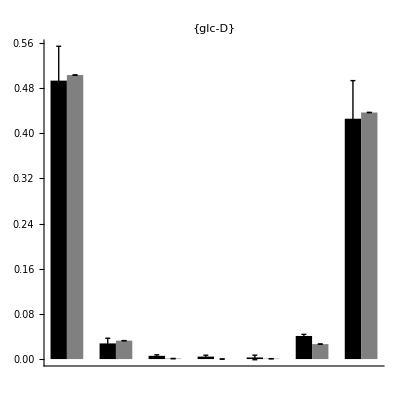
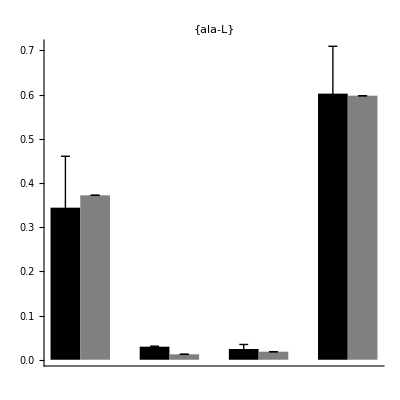
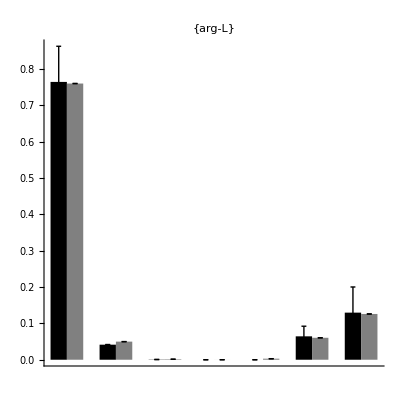
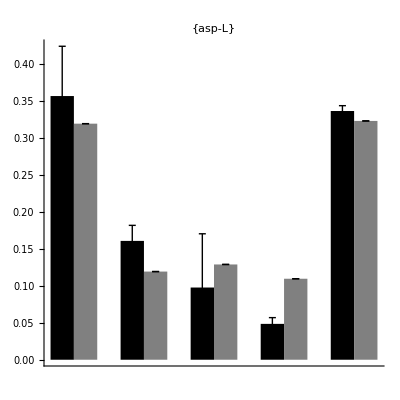
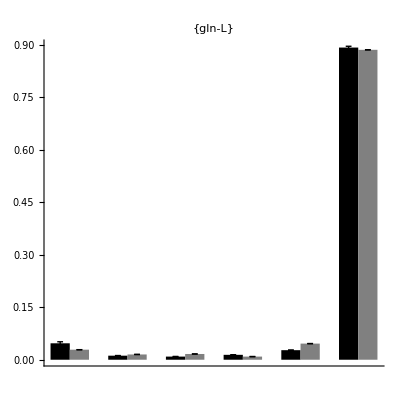
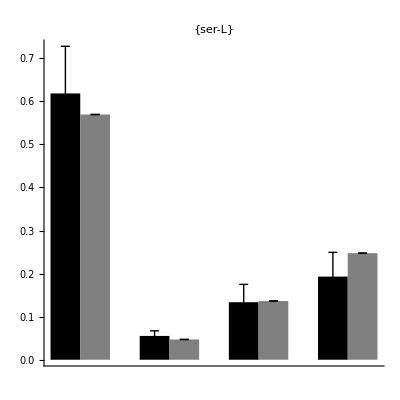
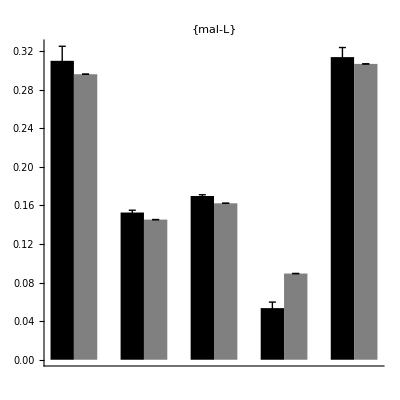
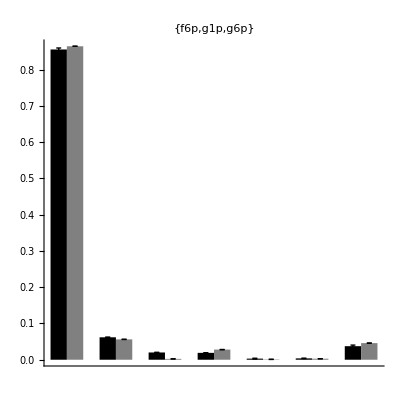

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetIds⟦i⟧],
{i,Length[measuredMetIds]}]
```

Scatter plot of all fitted MIDs

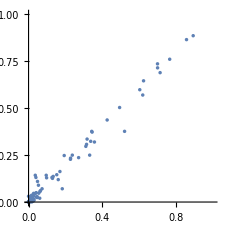

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

### Fluxes

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 91 reactions, 36 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 35.3607 | 0. | 35.3607
<Reaction ACITL> | 0.001 | 0. | 0.001
<Reaction ACOAHi> | 173.219 | 0. | 173.219
<Reaction ACONTm(rev)> | 227.566 | 0.001 | 227.565
<Reaction ACRNtm> | 69.0125 | 0. | 69.0125
<Reaction ACS> | 242.231 | 0. | 242.231
<Reaction ADK1> | 242.233 | 0. | 242.233
<Reaction AKGDm(rev)> | 10000. | 9822.54 | 177.462
<Reaction AKGtm(rev)> | 0.001 | 0.001 | 0.
<Reaction ALATA_L> | 29.5227 | 0. | 29.5227
<Reaction ARGN> | 0.00175871 | 0. | 0.00175871
<Reaction ARGSL> | 0.00175871 | 0. | 0.00175871
<Reaction ARGSS> | 0.00175871 | 0. | 0.00175871
<Reaction ASPTA(rev)> | 10000. | 9996. | 3.99534
<Reaction ASPTAm(rev)> | 0.002 | 0.001 | 0.001
<Reaction ASPtm> | 0.001 | 0. | 0.001
<Reaction ATPS4m> | 2002.74 | 0. | 2002.74
<Reaction ATPtm(rev)> | 2133.78 | 0.001 | 2133.77
<Reaction CBPSam> | 0.00175871 | 0. | 0.00175871
<Reaction CELLWORK> | 0.0441904 | 0. | 0.0441904
<Reaction CITtm> | 0.001 | 0. | 0.001
<Reaction CO2tm(rev)> | 9482.85 | 10000. | -517.153
<Reaction CRNtim> | 69.0125 | 0. | 69.0125
<Reaction CSm> | 227.566 | 0. | 227.566
<Reaction CSNATm> | 69.0125 | 0. | 69.0125
<Reaction CSNATr> | 69.0125 | 0. | 69.0125
<Reaction CYOOm> | 436.041 | 0. | 436.041
<Reaction CYOR-u10m> | 872.082 | 0. | 872.082
<Reaction ENO(rev)> | 210.849 | 0.001 | 210.848
<Reaction FBA(rev)> | 342.618 | 118.868 | 223.75
<Reaction FBP> | 1775.27 | 0. | 1775.27
<Reaction FUMm> | 177.465 | 0. | 177.465
<Reaction FUMtm> | 0.00175871 | 0. | 0.00175871
<Reaction G3PD1> | 203.134 | 0. | 203.134
<Reaction G6PPer> | 40.7229 | 0. | 40.7229
<Reaction G6Pter(rev)> | 0.001 | 129.174 | -129.173
<Reaction GAPD(rev)> | 244.367 | 0.001 | 244.366
<Reaction GHMT2r(rev)> | 13.6731 | 13.6731 | 0.
<Reaction GLCter> | 40.7219 | 0. | 40.7219
<Reaction GLNtm> | 32.6969 | 0. | 32.6969
<Reaction GLUDxm(rev)> | 0.001 | 50.1054 | -50.1044
<Reaction GLUNm(rev)> | 36.9485 | 4.25166 | 32.6969
<Reaction GLUt2m(rev)> | 4.87793 | 87.6782 | -82.8003
<Reaction GLYCOGEN_BREAK> | 169.896 | 0. | 169.896
<Reaction GLYCPH> | 203.135 | 0. | 203.135
<Reaction GLYK> | 0.001 | 0. | 0.001
<Reaction GTHS> | 10.8855 | 0. | 10.8855
<Reaction H2Oter> | 40.7229 | 0. | 40.7229
<Reaction H2Otm(rev)> | 3.00206 | 2443.77 | -2440.77
<Reaction HCO3Em> | 46.428 | 0. | 46.428
<Reaction HEX1> | 94.5766 | 0. | 94.5766
<Reaction Htm2(rev)> | 0.001 | 2245.9 | -2245.9
<Reaction ICDHxm(rev)> | 238.019 | 10.454 | 227.565
<Reaction LDH_L(rev)> | 71.0725 | 0.001 | 71.0715
<Reaction MALtm> | 3.67736 | 0. | 3.67736
<Reaction MDH> | 3.67736 | 0. | 3.67736
<Reaction MDHm(rev)> | 181.143 | 0.001 | 181.142
<Reaction MMEm> | 0.001 | 0. | 0.001
<Reaction MMMm> | 0.001 | 0. | 0.001
<Reaction MMSAD1m> | 0.001 | 0. | 0.001
<Reaction NADH2-u10m> | 694.619 | 0. | 694.619
<Reaction NADH_REDOX> | 0.001 | 0. | 0.001
<Reaction NDPK1> | 0.318976 | 0. | 0.318976
<Reaction NH4tm(rev)> | 22.2658 | 4.8565 | 17.4093
<Reaction O2tm> | 436.041 | 0. | 436.041
<Reaction OCBTm> | 0.00175871 | 0. | 0.00175871
<Reaction ORNt4m> | 0.00175871 | 0. | 0.00175871
<Reaction PCm> | 46.4253 | 0. | 46.4253
<Reaction PDHm> | 158.554 | 0. | 158.554
<Reaction PEPCK> | 0.318976 | 0. | 0.318976
<Reaction PFK> | 1999.02 | 0. | 1999.02
<Reaction PGCD> | 33.518 | 0. | 33.518
<Reaction PGI(rev)> | 223.751 | 0.001 | 223.75
<Reaction PGK(rev)> | 244.367 | 0.001 | 244.366
<Reaction PGM(rev)> | 210.849 | 0.001 | 210.848
<Reaction PGMTer> | 169.896 | 0. | 169.896
<Reaction PIt2m> | 2133.77 | 0. | 2133.77
<Reaction PIter> | 40.7229 | 0. | 40.7229
<Reaction PPA> | 242.233 | 0. | 242.233
<Reaction PPCOACm> | 0.001 | 0. | 0.001
<Reaction PROTDEG_ALA> | 11.3434 | 0. | 11.3434
<Reaction PROTDEG_ARG> | 0.001 | 0. | 0.001
<Reaction PSERT> | 33.518 | 0. | 33.518
<Reaction PSP_L> | 33.518 | 0. | 33.518
<Reaction PYK> | 211.167 | 0. | 211.167
<Reaction PYRt2m(rev)> | 204.98 | 0.001 | 204.979
<Reaction SERHL> | 35.3607 | 0. | 35.3607
<Reaction SUCD1m> | 177.463 | 0. | 177.463
<Reaction SUCOASm> | 177.463 | 0. | 177.463
<Reaction TPI(rev)> | 20.6169 | 0.001 | 20.6159
<Reaction ARG_tmL> | 0.001 | 0. | 0.001

```mathematica
MetaboliteProducers[net,Metabolite["glc-D","Cytosol","Uptake"]]
```

{{<Reaction GLCter>,1}}

Boundary fluxes

```mathematica
TableForm[
BoundaryFlux[fluxGams],
TableHeadings->{BoundaryFluxNames[bnet],None}]
```

2mop_IN | 0.001
ac_IN | 69.0115
ala-L_IN | 18.1792
arg-L_IN | 0.0030113
asp-L_IN | 10000.
co2_IN | 9482.53
energy_IN | 0.001
glc-D_IN | 53.8547
gln-L_IN | 32.6969
glucys_IN | 10.8855
gly_IN | 10.8855
glyc_IN | 0.001
glycogen_IN | 169.896
h2o_IN | 0.001
h_IN | 0.00127005
nh4_IN | 0.001
o2_IN | 436.041
pi_IN | 0.001
prot_ala_IN | 11.3434
prot_arg_IN | 0.001
ser-L_IN | 1.84367
arg-L_OUT | 0.0040113
asp-L_OUT | 9996.
co2_OUT | 10000.
energy_OUT | 0.0451904
glc-D_OUT | 0.001
glu-L_OUT | 82.8003
glyc_OUT | 203.135
gthrd_OUT | 10.8855
h2o_OUT | 183.482
h_OUT | 62.915
lac-L_OUT | 71.0715
nh4_OUT | 17.9524
pi_OUT | 0.001
ser-L_OUT | 0.001
urea_OUT | 0.00175871

Fitted flux measurements

```mathematica
Block[{ix},
ix=ReindexList[measReactions,BoundaryFluxNames[bnet]];
TableForm[
Transpose[{fluxMixing.BoundaryFlux[fluxGams]⟦ix⟧,mediumConcDiffMean*mediumVolume/cultureTime*10^9}],
TableHeadings->{measFluxNames,{"fitted","measured"}}]]
```

| fitted | measured
ala-L | -18.1792 | -18.352
arg-L | 0.001 | -0.794304
asp-L | -3.9961 | -4.02026
gln-L | -32.6969 | -30.8959
gly | -10.8855 | -11.7977
ser-L | -1.84267 | -1.88277
glc-D | -53.8537 | -86.8352
lac-L | 71.0715 | 67.7083

### Check objective

```mathematica
Map[Max[StandardDeviation[#],minSD]&,midsToFit]
```

{0.0674452,0.116349,0.0980459,0.0726937,0.03,0.10951,0.03,0.03,0.0446224,0.03,0.03,0.0662253,0.0331833,0.0407826}

```mathematica
midChi=(fittedMIDs-Mean/@midsToFit)/Map[Max[StandardDeviation[#],minSD]&,midsToFit];
TableForm[midChi,TableHeadings->{measuredMetNames,None}]
```

glc-D | 0.146226 | 0.0732508 | -0.0715172 | -0.0645368 | -0.0323507 | -0.214326 | 0.163254
ala-L | 0.240079 | -0.148453 | -0.0517835 | -0.0398419 |  |  | 
arg-L | -0.0454283 | 0.0856873 | 0.00757772 | 0.000777226 | 0.0291301 | -0.0405456 | -0.0371984
asp-L | -0.513903 | -0.570598 | 0.429156 | 0.839905 | -0.18456 |  | 
gln-L | -0.607234 | 0.116155 | 0.248025 | -0.167803 | 0.625596 | -0.21474 | 
ser-L | -0.446665 | -0.0751967 | 0.0251606 | 0.496702 |  |  | 
mal-L | -0.463868 | -0.244238 | -0.253102 | 1.19571 | -0.234501 |  | 
f6p__g1p__g6p | 0.295135 | -0.191913 | -0.587873 | 0.300885 | -0.0687803 | -0.0298237 | 0.28237
orn | -0.778634 | -0.00359463 | 0.00635806 | -0.00730846 | 0.43866 | 0.344519 | 
citr-L | 0.0146966 | 0.298121 | -0.505941 | 0.023815 | 0.47468 | -0.799504 | 0.494132
glyc3p | 1.23477 | -0.736436 | -0.702778 | 0.204448 |  |  | 
akg | -1.22952 | 1.37444 | 1.60091 | -0.0388127 | 0.464272 | -2.17129 | 
glu-L | 0.378802 | 0.119977 | 1.40975 | -3.37248 | 0.435591 | 1.02835 | 
gly | 0.440813 | -0.986899 | 0.546086 |  |  |  |

```mathematica
Flatten[midChi]//Length
```

77

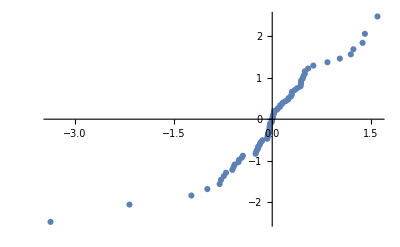

```mathematica
Block[{qObs,q0,labels,ix},
qObs=Flatten[midChi];
labels=Flatten[Table[measuredMetNames⟦i⟧,{i,Length[midChi]},{Length[midChi⟦i⟧]}]];
ix=Ordering[qObs];
q0=Quantile[NormalDistribution[0,1],N[(Range[Length[qObs]]-1/2)/Length[qObs]]];
ListPlot[
Thread[Tooltip[Transpose[{qObs⟦ix⟧,q0}],labels⟦ix⟧]],
PlotRange->All]]
```

Chi square

```mathematica
TableForm[midChi^2,TableHeadings->{measuredMetNames,None}]
```

glc-D | 0.0213821 | 0.00536568 | 0.00511471 | 0.004165 | 0.00104657 | 0.0459358 | 0.0266519
ala-L | 0.0576377 | 0.0220383 | 0.00268153 | 0.00158738 |  |  | 
arg-L | 0.00206373 | 0.00734231 | 0.0000574219 | 6.0408×10^-7 | 0.000848563 | 0.00164395 | 0.00138372
asp-L | 0.264097 | 0.325582 | 0.184175 | 0.70544 | 0.0340623 |  | 
gln-L | 0.368733 | 0.013492 | 0.0615166 | 0.0281577 | 0.39137 | 0.0461131 | 
ser-L | 0.19951 | 0.00565455 | 0.000633054 | 0.246712 |  |  | 
mal-L | 0.215174 | 0.0596522 | 0.0640608 | 1.42972 | 0.0549909 |  | 
f6p__g1p__g6p | 0.0871045 | 0.0368308 | 0.345594 | 0.0905317 | 0.00473073 | 0.000889451 | 0.0797331
orn | 0.606271 | 0.0000129214 | 0.000040425 | 0.0000534136 | 0.192422 | 0.118694 | 
citr-L | 0.00021599 | 0.0888763 | 0.255977 | 0.000567152 | 0.225321 | 0.639207 | 0.244167
glyc3p | 1.52465 | 0.542338 | 0.493897 | 0.0417991 |  |  | 
akg | 1.51173 | 1.88908 | 2.56293 | 0.00150642 | 0.215548 | 4.7145 | 
glu-L | 0.143491 | 0.0143944 | 1.98741 | 11.3736 | 0.18974 | 1.05751 | 
gly | 0.194316 | 0.973971 | 0.29821 |  |  |  |

```mathematica
Total[Flatten[midChi^2]]
```

37.6537

Flux errors

```mathematica
fluxChi=Block[{ix},
ix=ReindexList[measReactions,BoundaryFluxNames[bnet]];
(fluxMixing.BoundaryFlux[fluxGams]⟦ix⟧-mediumConcDiffMean*mediumVolume/cultureTime*10^9)/(mediumConcDiffMean*mediumVolume/cultureTime*10^9)]
```

{-0.00941508,-1.00126,-0.00600961,0.0582912,-0.0773234,-0.0212963,-0.379816,0.0496715}

```mathematica
Total[Flatten[{midChi^2,fluxChi^2}]]
```

38.8129